```mathematica
ClearAll["Global`*"]
```

## Model Domain

### Analytic Region

```mathematica
Ω=RegionDifference[
Rectangle[{0,-1},{8,1}],
Rectangle[{4,1/2},{6,1}]
];
```

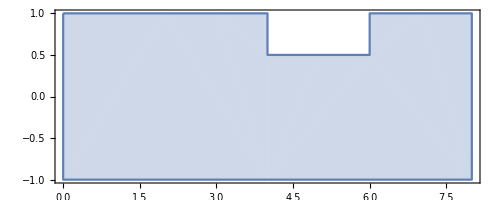

```mathematica
RegionPlot[Ω,AspectRatio->Automatic]
```

### Triangulation

```mathematica
NotebookEvaluate[NotebookDirectory[]<>"../../Tools/Mathematica/triangulation.nb"]
```

```mathematica
𝒯=create𝒯fromRegion[Ω,1.];
```

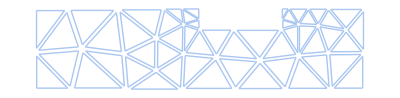

```mathematica
highlight@𝒯
```

```mathematica
SetDirectory@NotebookDirectory[];
export@𝒯
```

mesh.ntn

## Input Data for PDE

```mathematica
<<Notation`
Symbolize[ℛℯ^_]
Symbolize[n̄]
```

α u + (w . ∇)u - ℛℯ^-1 Δ u + ∇p = f,
∇ . u = g,

u|_Γ_in = u_in, u|_Γ_0 = 0,
(ℛℯ^-1(∂u)/(∂n̂) - p n̂)|_Γ_out = h

Velocity field:

```mathematica
(*u@{x_,y_}:={
1/600(1-y)(1+y)(x-4)^2(x-6)^2,
1/40(1-y)(1+y)(y-1/2)(x-4)(x-6)
}*)
u@{x_,y_}:={
x^3+y-1,
3y
}
```

Pressure distribution:

```mathematica
p@{x_,y_}:=2x y
```

Other parameters:

```mathematica
α=1;
```

```mathematica
w@{x_,y_}:={
x,
y
}
```

```mathematica
ℛℯ^-1=2;
```

```mathematica
n̂@{x,y}:={
1,
0
}
```

### Computed Data

Force term:

```mathematica
f@{x_,y_}=FullSimplify[α u@{x,y}+(w@{x,y}.{D[#, x],D[#, y]})&@u@{x,y}-ℛℯ^-1 Laplacian[u@{x,y},{x,y}]+Grad[p@{x,y},{x,y}]];
InputForm@f@{x,y}/.{x->p[0],y->p[1]}
```

{-1 + 4*p[0]*(-3 + p[0]^2) + 4*p[1], 2*(p[0] + 3*p[1])}

“Continuity” term:

```mathematica
g@{x_,y_}=FullSimplify@Div[u@{x,y},{x,y}]
```

-1/600 (-6+x) (-4+x) (5-4 x-15 y+(25+4 x) y^2)

Neumann value:

```mathematica
MatrixForm@Grad[u@{x,y},{x,y}]
```

(1/300 (-6+x)^2 (-4+x) (1-y) (1+y)+1/300 (-6+x) (-4+x)^2 (1-y) (1+y) | 1/600 (-6+x)^2 (-4+x)^2 (1-y)-1/600 (-6+x)^2 (-4+x)^2 (1+y)
1/40 (-6+x) (1-y) (-1/2+y) (1+y)+1/40 (-4+x) (1-y) (-1/2+y) (1+y) | 1/40 (-6+x) (-4+x) (1-y) (-1/2+y)+1/40 (-6+x) (-4+x) (1-y) (1+y)-1/40 (-6+x) (-4+x) (-1/2+y) (1+y))

```mathematica
h@{x_,y_}=FullSimplify[(ℛℯ^-1 Grad[u@{x,y},{x,y}]-p@{x,y}IdentityMatrix@2).n̂@{x,y}]
```

{2 x (3 x-y),0}

### Plot

```mathematica
Show[StreamDensityPlot[u@{x,y},{x,y}∈Ω,
ColorFunction->"DeepSeaColors",
PlotLegends->Automatic,
AspectRatio->Automatic
],ImageSize->Full]
```

StreamDensityPlot::idomdim: Ω does not have a valid dimension as a plotting domain.

Show::gtype: StreamDensityPlot is not a type of graphics.

Show[StreamDensityPlot[u[{x,y}],{x,y}∈Ω,ColorFunction→DeepSeaColors,PlotLegends→Automatic,AspectRatio→Automatic],ImageSize→Full]

```mathematica
First@u@{x,y}
```

u1[{x,y}]

```mathematica
Plot3D[Last@u@{x,y},{x,y}∈Ω,
BoxRatios->Automatic,
PlotRange->{Automatic,Automatic,{-.5,.5}},
Mesh->None
]
```

Plot3D::idomdim: Ω does not have a valid dimension as a plotting domain.

Plot3D[Last[u[{x,y}]],{x,y}∈Ω,BoxRatios→Automatic,PlotRange→{Automatic,Automatic,{-0.5,0.5}},Mesh→None]